```mathematica
pivot[iStar_,jStar_,tab_]:=(
newTab=tab;
rows=Dimensions[tab][[1]];
cols=Dimensions[tab][[2]];
(* switch variables *)
newTab[[1,jStar]]=tab[[iStar,cols]];
newTab[[iStar,cols]]=tab[[1,jStar]];
For[ii=2,ii<=rows,ii++,
For[jj=1,jj<cols,jj++,
{
If[ii==iStar&&jj==jStar,newTab[[ii,jj]]=1/tab[[iStar,jStar]]];
If[ii==iStar&&jj!=jStar,newTab[[ii,jj]]=-tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj==jStar,newTab[[ii,jj]]=tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj!=jStar,newTab[[ii,jj]]=tab[[ii,jj]]-tab[[iStar,jj]]tab[[ii,jStar]]/tab[[iStar,jStar]]];
}
]
];
Return[newTab]
)
```

```mathematica
(* min z = 6x1+1x2-2
-3x1+2x2>=-12
2x1+5x2>=-20
-x1-6x2>=3
1x1-2x2>=-4
12x1+2x2>=-60
 *)
```

```mathematica
a0={"u1","u2","u3","u4",1," "}
a1={-3,3,2,-2,12,"s1"}
a2={2,-2,5,-5,20,"s2"}
a3={-1,1,-6,6,-3,"s3"}
a4={1,-1,-2,2,4,"s4"}
a5={12,-12,2,-2,60,"s5"}
z={6,-6,1,-1,-2,"z"}
a = {a0,a1,a2,a3,a4,a5,z}
g1[x1_, x2_] := -3x1+2x2; b1 = -12; 
g2[x1_, x2_] := 2x1+5x2; b2 = -20; 
g3[x1_, x2_] := -x1-6x2; b3 = 3; 
g4[x1_, x2_] := 1x1-2x2; b4= -4; 
g5[x1_, x2_] := 12x1+2x2;b5 = -60; 
g1[x1_]=x2/.Solve[g1[x1,x2] == b1] [[1,1]] 
g2[x1_]=x2/.Solve[g2[x1,x2] == b2] [[1,1]] 
g3[x1_]=x2/.Solve[g3[x1,x2] == b3] [[1,1]] 
g4[x1_]=x2/.Solve[g4[x1,x2] == b4] [[1,1]] 
g5[x1_]=x2/.Solve[g5[x1,x2] == b5] [[1,1]] 

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x]}, {x,-12,12}, PlotHighlighting->None, AspectRatio->Automatic, PlotRange-> {-15,15}, PlotLegends -> Automatic]
```

{u1,u2,u3,u4,1, }

{-3,3,2,-2,12,s1}

{2,-2,5,-5,20,s2}

{-1,1,-6,6,-3,s3}

{1,-1,-2,2,4,s4}

{12,-12,2,-2,60,s5}

{6,-6,1,-1,-2,z}

{{u1,u2,u3,u4,1, },{-3,3,2,-2,12,s1},{2,-2,5,-5,20,s2},{-1,1,-6,6,-3,s3},{1,-1,-2,2,4,s4},{12,-12,2,-2,60,s5},{6,-6,1,-1,-2,z}}

-6+(3 x1)/2

-4-(2 x1)/5

-1/2-x1/6

2+x1/2

-30-6 x1

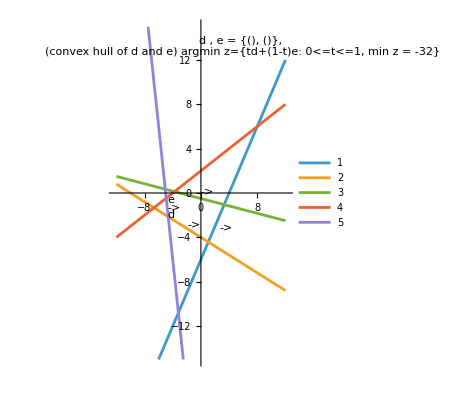

```mathematica
b = pivot[3,2,a];
Print[MatrixForm[b]]
```

(u1 | s2 | u3 | u4 | 1 |  
0 | -3/2 | 19/2 | -19/2 | 42 | s1
1 | -1/2 | 5/2 | -5/2 | 10 | u2
0 | -1/2 | -7/2 | 7/2 | 7 | s3
0 | 1/2 | -9/2 | 9/2 | -6 | s4
0 | 6 | -28 | 28 | -60 | s5
0 | 3 | -14 | 14 | -62 | z)

```mathematica
Sort[{2*42/18 ,2*10/5}]
Ordering[{2*42/18 ,2*10/5}]
c = pivot[2,4,b]
Print[MatrixForm[c]]
```

{4,14/3}

{2,1}

{{u1,s2,u3,s1,1, },{0,-3/19,1,-2/19,84/19,u4},{1,-2/19,0,5/19,-20/19,u2},{0,-20/19,0,-7/19,427/19,s3},{0,-4/19,0,-9/19,264/19,s4},{0,30/19,0,-56/19,1212/19,s5},{0,15/19,0,-28/19,-2/19,z}}

(u1 | s2 | u3 | s1 | 1 |  
0 | -3/19 | 1 | -2/19 | 84/19 | u4
1 | -2/19 | 0 | 5/19 | -20/19 | u2
0 | -20/19 | 0 | -7/19 | 427/19 | s3
0 | -4/19 | 0 | -9/19 | 264/19 | s4
0 | 30/19 | 0 | -56/19 | 1212/19 | s5
0 | 15/19 | 0 | -28/19 | -2/19 | z)

```mathematica
Sort[{5*4/2, 5*21/7, 5*12/9, 5*52/56}]
Ordering[{5*4/2, 5*21/7, 5*12/9, 5*52/56}]
d= pivot[6,4,c]
Print[MatrixForm[d]]
```

{65/14,20/3,10,15}

{4,3,1,2}

{{u1,s2,u3,s5,1, },{0,-3/14,1,1/28,15/7,u4},{1,1/28,0,-5/56,65/14,u2},{0,-5/4,0,1/8,29/2,s3},{0,-13/28,0,9/56,51/14,s4},{0,15/28,0,-19/56,303/14,s1},{0,0,0,1/2,-32,z}}

(u1 | s2 | u3 | s5 | 1 |  
0 | -3/14 | 1 | 1/28 | 15/7 | u4
1 | 1/28 | 0 | -5/56 | 65/14 | u2
0 | -5/4 | 0 | 1/8 | 29/2 | s3
0 | -13/28 | 0 | 9/56 | 51/14 | s4
0 | 15/28 | 0 | -19/56 | 303/14 | s1
0 | 0 | 0 | 1/2 | -32 | z)

```mathematica
e=pivot[5,2,d]
Print[MatrixForm[e]] (*because there is a level set*)
```

{{u1,s4,u3,s5,1, },{0,6/13,1,-1/26,6/13,u4},{1,-1/13,0,-1/13,64/13,u2},{0,35/13,0,-4/13,61/13,s3},{0,-28/13,0,9/26,102/13,s2},{0,-15/13,0,-2/13,336/13,s1},{0,0,0,1/2,-32,z}}

(u1 | s4 | u3 | s5 | 1 |  
0 | 6/13 | 1 | -1/26 | 6/13 | u4
1 | -1/13 | 0 | -1/13 | 64/13 | u2
0 | 35/13 | 0 | -4/13 | 61/13 | s3
0 | -28/13 | 0 | 9/26 | 102/13 | s2
0 | -15/13 | 0 | -2/13 | 336/13 | s1
0 | 0 | 0 | 1/2 | -32 | z)

```mathematica
(*How to pivot from intersection to intersection geometrically: 
 We want to go from intersection of s4, s5 to s2 s4 so we pivot on s5 s2. Think of it like this: we had s4,s5 at the top of the tableau and we want it to be s4,s2 at the top of the tableau. We pivot on the line we are leaving and the line we are arriving at. leaving = Jstar and arriving = istar.*)
f = pivot[5,4, d]
Print[MatrixForm[f]]
```

{{u1,s2,u3,s4,1, },{0,-1/9,1,2/9,4/3,u4},{1,-2/9,0,-5/9,20/3,u2},{0,-8/9,0,7/9,35/3,s3},{0,26/9,0,56/9,-68/3,s5},{0,-4/9,0,-19/9,88/3,s1},{0,13/9,0,28/9,-130/3,z}}

(u1 | s2 | u3 | s4 | 1 |  
0 | -1/9 | 1 | 2/9 | 4/3 | u4
1 | -2/9 | 0 | -5/9 | 20/3 | u2
0 | -8/9 | 0 | 7/9 | 35/3 | s3
0 | 26/9 | 0 | 56/9 | -68/3 | s5
0 | -4/9 | 0 | -19/9 | 88/3 | s1
0 | 13/9 | 0 | 28/9 | -130/3 | z)